## Functions for implementing TWA and DTWA

```mathematica
samples = 10000;

J[i_,j_]:=If[ Abs[i-j]==1,1,0];
S11={{1,1,1},{-1,-1,1},{1,-1,-1},{-1,1,-1}};
SAll=Join[S11,-S11];
```

```mathematica
dtwaEnsemble[θinit_,num_,rs_]:=Module[{paulis,ρ,wigner,ws},
paulis=Table[PauliMatrix[i],{i,3}];
ρ[r_]:=(IdentityMatrix[2]+r.paulis)/2;
wigner[r_,θ_]:=Tr[ρ[{Sin[θ],0,Cos[θ]}].ρ[r]]/2;
ws=wigner[#,θinit]&/@rs;

Table[RandomChoice[Abs[ws]->1/2 rs],{samples},{num}]
];
scaleFactor[θinit_,rs_]:=Module[{paulis,ρ,wigner,ws},
paulis=Table[PauliMatrix[i],{i,3}];
ρ[r_]:=(IdentityMatrix[2]+r.paulis)/2;
wigner[i_,θ_]:=Tr[ρ[{Sin[θ],0,Cos[θ]}].ρ[rs[[i]]]]/2;
ws=wigner[#,θinit]&/@Range[Length[rs]];
Sign[ws]*Total[Abs[ws]]/Total[ws]
];

(* Both definitions of twaEnsemble take similar amount of time. *)
(*twaEnsemble[θinit_]:=
Table[RotationMatrix[θinit,{0,1,0}].{RandomVariate[NormalDistribution[0,1/2]],RandomVariate[NormalDistribution[0,1/2]],1/2},{samples},{num}];*)
twaEnsemble[θinit_,num_]:=Module[{rands=RandomVariate[NormalDistribution[0,1/2],2num*samples],Sxs,Sys,Szs,Ss},
Sxs=Take[rands,num*samples]; Sys=Take[rands,-num*samples];Szs=Table[1/2,{num*samples}];
ArrayReshape[(RotationMatrix[θinit,{0,1,0}].#)&/@Transpose[{Sxs,Sys,Szs}],{samples,num,3}]
];
```

```mathematica
(* The following two functions for dTWA *)
onSiteOpsIsing[ensemble_,{phasepoints_,scaleFactors_},num_,h_,tlist_]:=Module[{initCond,diffEqs,vars,trajectories,factors,tmax=tlist[[-1]],interpol},
1/samples Sum[
initCond=Flatten[Table[{x[i][0]==ensemble[[trajectory,i,1]],y[i][0]==ensemble[[trajectory,i,2]],z[i][0]==ensemble[[trajectory,i,3]]},{i,num}]];
diffEqs=Flatten[Table[{x[i]'[t]==y[i][t]*(Sum[J[i,j]z[j][t],{j,num}]),y[i]'[t]==h z[i][t]-x[i][t]*(Sum[J[i,j]z[j][t],{j,num}]),z[i]'[t]==-h y[i][t]},{i,num}]];
vars=Flatten[Table[{x[i][t],y[i][t],z[i][t]},{i,num}]];
trajectories=NDSolveValue[Join[initCond,diffEqs],vars,{t,0.,tmax}];
factors=scaleFactors[[Position[phasepoints,2ensemble[[trajectory,#]]][[1,1]]]]&/@Range[num];
interpol=Take[trajectories,{3 num/2+1,3 num/2+3}]*Product[factors[[i]],{i,num}];
Table[interpol[[i]]/.t->#,{i,3}]&/@tlist
,{trajectory,1,samples}]
];
corrsIsing[ensemble_,{phasepoints_,scaleFactors_},num_,h_,tlist_]:=Module[{initCond,diffEqs,vars,trajectories,factors,interpol,tmax=tlist[[-1]]},
1/samples Sum[
initCond=Flatten[Table[{x[i][0]==ensemble[[trajectory,i,1]],y[i][0]==ensemble[[trajectory,i,2]],z[i][0]==ensemble[[trajectory,i,3]]},{i,num}]];
diffEqs=Flatten[Table[{x[i]'[t]==y[i][t]*(Sum[J[i,j]z[j][t],{j,num}]),y[i]'[t]==h z[i][t]-x[i][t]*(Sum[J[i,j]z[j][t],{j,num}]),z[i]'[t]==-h y[i][t]},{i,num}]];
vars=Flatten[Table[{x[i][t],y[i][t],z[i][t]},{i,num}]];
trajectories=NDSolveValue[Join[initCond,diffEqs],vars,{t,0.,tmax}];
factors=scaleFactors[[Position[phasepoints,2ensemble[[trajectory,#]]][[1,1]]]]&/@Range[num];
interpol=KroneckerProduct[Take[trajectories,{3 num/2-2,3 num/2}],Take[trajectories,{3 num/2+1,3 num/2+3}]]*Product[factors[[i]],{i,num}];
Table[interpol[[i,j]]/.t->#,{i,3},{j,3}]&/@tlist
,{trajectory,1,samples}]
];
(* The following two functions for TWA *)
onSiteOpsIsing[ensemble_,num_,h_,tlist_]:=Module[{initCond,diffEqs,vars,trajectories,tmax=tlist[[-1]],interpol},
1/samples Sum[
initCond=Flatten[Table[{x[i][0]==ensemble[[trajectory,i,1]],y[i][0]==ensemble[[trajectory,i,2]],z[i][0]==ensemble[[trajectory,i,3]]},{i,num}]];
diffEqs=Flatten[Table[{x[i]'[t]==y[i][t]*(Sum[J[i,j]z[j][t],{j,num}]),y[i]'[t]==h z[i][t]-x[i][t]*(Sum[J[i,j]z[j][t],{j,num}]),z[i]'[t]==-h y[i][t]},{i,num}]];
vars=Flatten[Table[{x[i][t],y[i][t],z[i][t]},{i,num}]];
trajectories=NDSolveValue[Join[initCond,diffEqs],vars,{t,0.,tmax}];
interpol=Take[trajectories,{3 num/2+1,3 num/2+3}];
Table[interpol[[i]]/.t->#,{i,3}]&/@tlist
,{trajectory,1,samples}]
];
corrsIsing[ensemble_,num_,h_,tlist_]:=Module[{initCond,diffEqs,vars,trajectories,interpol,tmax=tlist[[-1]]},
1/samples Sum[
initCond=Flatten[Table[{x[i][0]==ensemble[[trajectory,i,1]],y[i][0]==ensemble[[trajectory,i,2]],z[i][0]==ensemble[[trajectory,i,3]]},{i,num}]];
diffEqs=Flatten[Table[{x[i]'[t]==y[i][t]*(Sum[J[i,j]z[j][t],{j,num}]),y[i]'[t]==h z[i][t]-x[i][t]*(Sum[J[i,j]z[j][t],{j,num}]),z[i]'[t]==-h y[i][t]},{i,num}]];
vars=Flatten[Table[{x[i][t],y[i][t],z[i][t]},{i,num}]];
trajectories=NDSolveValue[Join[initCond,diffEqs],vars,{t,0.,tmax}];
interpol=KroneckerProduct[Take[trajectories,{3 num/2-2,3 num/2}],Take[trajectories,{3 num/2+1,3 num/2+3}]];
Table[interpol[[i,j]]/.t->#,{i,3},{j,3}]&/@tlist
,{trajectory,1,samples}]
];
```

```mathematica
(* The following two functions for dTWA *)
onSiteOpsXY[ensemble_,{phasepoints_,scaleFactors_},num_,tlist_]:=Module[{initCond,diffEqs,vars,trajectories,factors,tmax=Max[tlist],interpol},
1/samples Sum[
initCond=Flatten[Table[{x[i][0]==ensemble[[trajectory,i,1]],y[i][0]==ensemble[[trajectory,i,2]],z[i][0]==ensemble[[trajectory,i,3]]},{i,num}]];
diffEqs=Flatten[Table[{x[i]'[t]==-z[i][t]*(Sum[J[i,j]y[j][t],{j,num}]),y[i]'[t]==z[i][t]*(Sum[J[i,j]x[j][t],{j,num}]),z[i]'[t]==Sum[J[i,j](x[i][t]y[j][t]-y[i][t]x[j][t]),{j,num}]},{i,num}]];
vars=Flatten[Table[{x[i][t],y[i][t],z[i][t]},{i,num}]];
trajectories=NDSolveValue[Join[initCond,diffEqs],vars,{t,0.,tmax}];
factors=scaleFactors[[Position[phasepoints,2ensemble[[trajectory,#]]][[1,1]]]]&/@Range[num];
interpol=Take[trajectories,{3 num/2+1,3 num/2+3}]*Product[factors[[i]],{i,num}];
Table[interpol[[i]]/.t->#,{i,3}]&/@tlist
,{trajectory,1,samples}]
];
corrsXY[ensemble_,{phasepoints_,scaleFactors_},num_,tlist_]:=Module[{initCond,diffEqs,vars,trajectories,factors,tmax=Max[tlist],interpol},
1/samples Sum[
initCond=Flatten[Table[{x[i][0]==ensemble[[trajectory,i,1]],y[i][0]==ensemble[[trajectory,i,2]],z[i][0]==ensemble[[trajectory,i,3]]},{i,num}]];
diffEqs=Flatten[Table[{x[i]'[t]==-z[i][t]*(Sum[J[i,j]y[j][t],{j,num}]),y[i]'[t]==z[i][t]*(Sum[J[i,j]x[j][t],{j,num}]),z[i]'[t]==Sum[J[i,j](x[i][t]y[j][t]-y[i][t]x[j][t]),{j,num}]},{i,num}]];
vars=Flatten[Table[{x[i][t],y[i][t],z[i][t]},{i,num}]];
trajectories=NDSolveValue[Join[initCond,diffEqs],vars,{t,0.,tmax}];
factors=scaleFactors[[Position[phasepoints,2ensemble[[trajectory,#]]][[1,1]]]]&/@Range[num];
interpol=KroneckerProduct[Take[trajectories,{3 num/2-2,3 num/2}],Take[trajectories,{3 num/2+1,3 num/2+3}]]*Product[factors[[i]],{i,num}];
Table[interpol[[i,j]]/.t->#,{i,3},{j,3}]&/@tlist
,{trajectory,1,samples}]
];
(* The following two functions for TWA *)
onSiteOpsXY[ensemble_,num_,tlist_]:=Module[{initCond,diffEqs,vars,trajectories,tmax=Max[tlist],interpol},
1/samples Sum[
initCond=Flatten[Table[{x[i][0]==ensemble[[trajectory,i,1]],y[i][0]==ensemble[[trajectory,i,2]],z[i][0]==ensemble[[trajectory,i,3]]},{i,num}]];
diffEqs=Flatten[Table[{x[i]'[t]==-z[i][t]*(Sum[J[i,j]y[j][t],{j,num}]),y[i]'[t]==z[i][t]*(Sum[J[i,j]x[j][t],{j,num}]),z[i]'[t]==Sum[J[i,j](x[i][t]y[j][t]-y[i][t]x[j][t]),{j,num}]},{i,num}]];
vars=Flatten[Table[{x[i][t],y[i][t],z[i][t]},{i,num}]];
trajectories=NDSolveValue[Join[initCond,diffEqs],vars,{t,0.,tmax}];
interpol=Take[trajectories,{3 num/2+1,3 num/2+3}];
Table[interpol[[i]]/.t->#,{i,3}]&/@tlist
,{trajectory,1,samples}]
];
corrsXY[ensemble_,num_,tlist_]:=Module[{initCond,diffEqs,vars,trajectories,tmax=Max[tlist],interpol},
1/samples Sum[
initCond=Flatten[Table[{x[i][0]==ensemble[[trajectory,i,1]],y[i][0]==ensemble[[trajectory,i,2]],z[i][0]==ensemble[[trajectory,i,3]]},{i,num}]];
diffEqs=Flatten[Table[{x[i]'[t]==-z[i][t]*(Sum[J[i,j]y[j][t],{j,num}]),y[i]'[t]==z[i][t]*(Sum[J[i,j]x[j][t],{j,num}]),z[i]'[t]==Sum[J[i,j](x[i][t]y[j][t]-y[i][t]x[j][t]),{j,num}]},{i,num}]];
vars=Flatten[Table[{x[i][t],y[i][t],z[i][t]},{i,num}]];
trajectories=NDSolveValue[Join[initCond,diffEqs],vars,{t,0.,tmax}];
interpol=KroneckerProduct[Take[trajectories,{3 num/2-2,3 num/2}],Take[trajectories,{3 num/2+1,3 num/2+3}]];
Table[interpol[[i,j]]/.t->#,{i,3},{j,3}]&/@tlist
,{trajectory,1,samples}]
];
```

## Functions for implementing Exact diagonalization

```mathematica
σ[i_,s_,size_]:=KroneckerProduct[IdentityMatrix[2^(i-1),SparseArray],SparseArray@PauliMatrix[s],IdentityMatrix[2^(size-i),SparseArray]];
HamiltonianIsing[h_,nmax_]:=-1./4 Sum[σ[i,3,nmax].σ[i+1,3,nmax],{i,nmax-1}]+h/2 Sum[σ[i,1,nmax],{i,nmax}];
HamiltonianXY[nmax_]:=-1./4 Sum[σ[i,1,nmax].σ[i+1,1,nmax]+σ[i,2,nmax].σ[i+1,2,nmax],{i,nmax-1}];

initialProductState::usage="Creates an initial product state with all spins pointing along |θ>.";
initialProductState[θ_,nmax_]:=KroneckerProduct@@Table[{{Cos[θ/2],Sin[θ/2]}},{i,nmax}]⟦1⟧;
stateDecomp[s_,eVecs_]:=Table[(s.Conjugate[eVecs⟦i⟧])eVecs⟦i⟧,{i,Length@eVecs}];

myEigensystem[h_]:=Eigensystem[h];

onsiteOpsIsingED[s_,nmax_,h_,tList_]:=Module[
{eVals,eVecs,sD,sT,σx,σy,σz,H},
H=HamiltonianIsing[h,nmax];
σx=σ[nmax/2+1,1,nmax]; σy=σ[nmax/2+1,2,nmax]; σz=σ[nmax/2+1,3,nmax];
{eVals,eVecs}=myEigensystem[H];
sD=stateDecomp[s,eVecs];
Table[
sT=Exp[-I eVals t].sD; (*sT=Normalize[sT];*)
1/2{Conjugate[sT].(σx.sT),Conjugate[sT].(σy.sT),Conjugate[sT].(σz.sT)},
{t,tList}]
];
corrsIsingED[s_,nmax_,h_,tList_]:=Module[
{eVals,eVecs,sD,sT,σxi,σyi,σzi,σxj,σyj,σzj,σσ,σi,σj,H},
H=HamiltonianIsing[h,nmax];
σxi=σ[nmax/2,1,nmax]; σyi=σ[nmax/2,2,nmax]; σzi=σ[nmax/2,3,nmax];
σxj=σ[nmax/2+1,1,nmax]; σyj=σ[nmax/2+1,2,nmax]; σzj=σ[nmax/2+1,3,nmax];
σσ={{σxi.σxj,σxi.σyj,σxi.σzj},{σyi.σxj,σyi.σyj,σyi.σzj},{σzi.σxj,σzi.σyj,σzi.σzj}};
σi={σxi,σyi,σzi}; σj={σxj,σyj,σzj};

{eVals,eVecs}=myEigensystem[H];
sD=stateDecomp[s,eVecs];
Table[
sT=Exp[-I eVals t].sD; (*sT=Normalize[sT];*)
1/4 Table[Conjugate[sT].(σσ[[i,j]].sT),{i,3},{j,3}](*-KroneckerProduct[Table[Conjugate[sT].(σi[[i]].sT),{i,3}],Table[Conjugate[sT].(σj[[j]].sT),{j,3}]]*),
{t,tList}]
];

onsiteOpsXYED[s_,nmax_,tList_]:=Module[
{eVals,eVecs,sD,sT,σx,σy,σz,H},
H=HamiltonianXY[nmax];
σx=σ[nmax/2+1,1,nmax]; σy=σ[nmax/2+1,2,nmax]; σz=σ[nmax/2+1,3,nmax];
{eVals,eVecs}=myEigensystem[H];
sD=stateDecomp[s,eVecs];
Table[
sT=Exp[-I eVals t].sD; (*sT=Normalize[sT];*)
{Conjugate[sT].(σx.sT),Conjugate[sT].(σy.sT),Conjugate[sT].(σz.sT)},
{t,tList}]
];
corrsXYED[s_,nmax_,tList_]:=Module[
{eVals,eVecs,sD,sT,σxi,σyi,σzi,σxj,σyj,σzj,σσ,σi,σj,H},
H=HamiltonianXY[nmax];
σxi=σ[nmax/2,1,nmax]; σyi=σ[nmax/2,2,nmax]; σzi=σ[nmax/2,3,nmax];
σxj=σ[nmax/2+1,1,nmax]; σyj=σ[nmax/2+1,2,nmax]; σzj=σ[nmax/2+1,3,nmax];
σσ={{σxi.σxj,σxi.σyj,σxi.σzj},{σyi.σxj,σyi.σyj,σyi.σzj},{σzi.σxj,σzi.σyj,σzi.σzj}};
σi={σxi,σyi,σzi}; σj={σxj,σyj,σzj};

{eVals,eVecs}=myEigensystem[H];
sD=stateDecomp[s,eVecs];
Table[
sT=Exp[-I eVals t].sD; (*sT=Normalize[sT];*)
Table[Conjugate[sT].(σσ[[i,j]].sT),{i,3},{j,3}]-KroneckerProduct[Table[Conjugate[sT].(σi[[i]].sT),{i,3}],Table[Conjugate[sT].(σj[[j]].sT),{j,3}]],
{t,tList}]
];
```

## Functions for plotting CMV

```mathematica
sc=2;(*Scales the axes of each plot*)
czoom=0.5;(*Scales the size of the bubble within each plot (depends on which j)*)

(*This is a misnomer, it gives the positions of the CMV's*)
bv={3.75,3.75,5}sc;

origin ={-sc,-sc,-sc};(*Sets the location of the axes origin*)
plot[function_,contour_, color_] := ContourPlot3D[function== contour,{x,- 4sc ,12sc},{y,-4sc,12sc},{z,-sc ,12sc}, SphericalRegion->True,ContourStyle->{Directive[color,Opacity[0.6],Specularity[White,30]]},Mesh->False,PlotPoints->70,PerformanceGoal->"Speed"];

p0=SphericalPlot3D[sc,{thet,π/2,π},{phi,π/2,3π/2},BaseStyle->FontSize->18,SphericalRegion->True,Boxed->False,Axes->True,Ticks->None,AxesOrigin->origin,AxesStyle->Thickness[0.0013],ViewPoint->{2,2,2},PlotStyle->{GrayLevel[0],Opacity[0]},MeshStyle->{Opacity[0]},PlotRange->{{origin⟦1⟧,origin⟦1⟧+10.75sc},{origin⟦2⟧,origin⟦2⟧+10.75sc},{origin⟦3⟧,origin⟦3⟧+10.75sc}},Method->{"ShrinkWrap"->True}(*,PlotLabel->Row[{"time: ",t}]*)]; (*the plot itself*)

CMVs[corrs_,tlist_?ListQ]:=Module[{r,polynomial,p1,p5,p4},
r={x,y,z}-bv;
(polynomial=(r.(corrs/.t->#).r)/(1+(r.r)^(3/2)/czoom^3);
Clear[x,y,z];
(*Generating the CMV*)
p1=plot[polynomial,0.01, Red]; (*graphs the figure*)
Clear[x,y,z];
p5=plot[polynomial,-0.01, Blue]; (*graphs the figure*)
Clear[x,y,z];
p4 = Graphics3D[{Text[Style["x",Bold,40],origin+{12sc+2,0,0}],Text[Style["y",Bold,40],origin+{0,12sc+2,0}],Text[Style["z",Bold,40],origin+{0,0,12sc+2}]}]; (* Axes labels *)

 Show[p0,p1,p5,(*Graphics3D[p2,ViewPoint->{2,2,2},PlotRange->{{0,3sc},{0,sc},{0,sc}}],Graphics3D[p3,ViewPoint->{2,2,2},PlotRange->{{0,3sc},{0,sc},{0,sc}}],*)(*p4,*)ImageSize->Medium,Spacings->{0,0}])&/@tlist];
CMVs[corrs_]:=Module[{r,polynomial,p1,p5,p4},
r={x,y,z}-bv;
(polynomial=(r.(#).r)/(1+(r.r)^(3/2)/czoom^3);
Clear[x,y,z];
(*Generating the CMV*)
p1=plot[polynomial,0.01, Red]; (*graphs the figure*)
Clear[x,y,z];
p5=plot[polynomial,-0.01, Blue]; (*graphs the figure*)
Clear[x,y,z];
p4 = Graphics3D[{Text[Style["x",Bold,40],origin+{12sc+2,0,0}],Text[Style["y",Bold,40],origin+{0,12sc+2,0}],Text[Style["z",Bold,40],origin+{0,0,12sc+2}]}]; (* Axes labels *)

 Show[p0,p1,p5,(*Graphics3D[p2,ViewPoint->{2,2,2},PlotRange->{{0,3sc},{0,sc},{0,sc}}],Graphics3D[p3,ViewPoint->{2,2,2},PlotRange->{{0,3sc},{0,sc},{0,sc}}],*)(*p4,*)ImageSize->Medium,Spacings->{0,0}])&/@corrs];
CMVs[corrs_,p_?NumericQ]:=Module[{r,polynomial,p1,p5,p4},
r={x,y,z}-bv;
(polynomial=(r.(#).r)/(1+(r.r)^(3/2)/czoom^3);
Clear[x,y,z];
(*Generating the CMV*)
p1=plot[polynomial,p, Red]; (*graphs the figure*)
Clear[x,y,z];
p5=plot[polynomial,-p, Blue]; (*graphs the figure*)
Clear[x,y,z];
p4 = Graphics3D[{Text[Style["x",Bold,40],origin+{12sc+2,0,0}],Text[Style["y",Bold,40],origin+{0,12sc+2,0}],Text[Style["z",Bold,40],origin+{0,0,12sc+2}]}]; (* Axes labels *)

 Show[p0,p1,p5,(*Graphics3D[p2,ViewPoint->{2,2,2},PlotRange->{{0,3sc},{0,sc},{0,sc}}],Graphics3D[p3,ViewPoint->{2,2,2},PlotRange->{{0,3sc},{0,sc},{0,sc}}],p4,*)ImageSize->Medium,Spacings->{0,0}])&/@corrs];
```

## Figures in our paper

### Figure 1

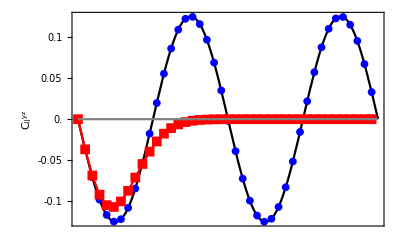

```mathematica
f1[t_]:=1/4 corrsExact[π/2,t/2][[2,3]];
f2[t_]:=1/4 corrsSAll[π/2,t/2][[2,3]];
f3[t_]:=1/4 corrsTWA[π/2,t/2][[2,3]];
ts=Range[0.,4π,0.3];

p=Plot[0,{t,0,4π},PlotStyle->Gray];
p1=Plot[f1[t],{t,0,4π},PlotRange->All,PlotStyle->Black, LabelStyle->Directive[FontSize->20],AxesOrigin->{0,-0.15},Frame->True,FrameTicks->{{Range[-0.1,0.1,0.05],None},{None,None}},FrameStyle->Thick,FrameLabel->{{Style["C_ij^yz",FontSize->20],None},{None,None}}];
p2=ListPlot[{#,f2[#]}&/@ts,PlotRange->All,PlotStyle->Blue,PlotMarkers-> {"●",8},LabelStyle->Directive[FontSize->20],AxesOrigin->{0,-0.15},Frame->True,FrameStyle->Thick];
p3=ListPlot[{#,f3[#]}&/@ts,PlotRange->All,Joined->True,PlotStyle->Red,PlotMarkers->{ "■",10},LabelStyle->Directive[FontSize->20],AxesOrigin->{0,-0.15},Frame->True,FrameStyle->Thick];

Show[p1,p2,p3,p]
Export["fig1b.pdf",%];
Clear[f1,f2,f3]
```

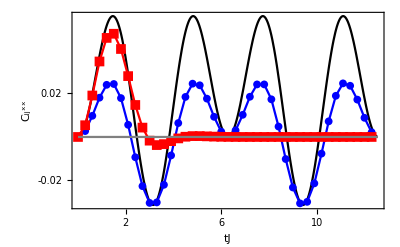

```mathematica
f1[t_]:=1/4 corrsExact[π/4,t/2][[1,1]];
f2[t_]:=1/4 corrsSAll[π/4,t/2][[1,1]];
f3[t_]:=1/4 corrsTWA[π/4,t/2][[1,1]];
ts=Range[0.,4π,0.3];

p=Plot[0,{t,0,4π},PlotStyle->Gray];
p1=Plot[f1[t],{t,0,4π},PlotRange->All,PlotStyle->Black, LabelStyle->Directive[FontSize->20],AxesOrigin->{0,-0.06},Frame->True,FrameTicks->{{Range[-0.06,0.06,0.04],None},{2Range[6],None}},FrameStyle->Thick,FrameLabel->{{Style["C_ij^xx",FontSize->20],None},{Style["tJ",FontSize->20],None}}];
p2=ListPlot[{#,f2[#]}&/@ts,PlotRange->All,Joined->True,PlotStyle->Blue,PlotMarkers-> {"●",8},LabelStyle->Directive[FontSize->20],AxesOrigin->{0,-0.06},Frame->True,FrameStyle->Thick];
p3=ListPlot[{#,f3[#]}&/@ts,PlotRange->All,Joined->True,PlotStyle->Red,PlotMarkers->{ "■",10},LabelStyle->Directive[FontSize->20],AxesOrigin->{0,-0.06},Frame->True,FrameStyle->Thick];

Show[p1,p2,p3,p]
Export["fig1c.pdf",%];
(* verified numerically that the results below are correct (Even though it appears that the black dTWA curve is factor-2 smaller than the other curves, suggesting I might have made a factor-2 mistake; But I haven't made any mistakes). *)
```

### Figs 2-5: Kenneth’s figures for these are correct.

### Figure 6

```mathematica
samples=10000;
dtwa=dtwaEnsemble[π/2,10,SAll];
twa=twaEnsemble[π/2,10];
factors=scaleFactor[π/2,SAll];

ts=Range[0.,3.5,0.7];
fIsingDTWA=onSiteOpsIsing[dtwa,{SAll,factors},10,1./3,ts];
gIsingDTWA=corrsIsing[dtwa,{SAll,factors},10,1./3,ts];

fIsingTWA=onSiteOpsIsing[twa,10,1./3,ts];
gIsingTWA=corrsIsing[twa,10,1./3,ts];

s=(KroneckerProduct@@Table[{{Cos[π/4.],Sin[π/4.]}},{10}])[[1]];
fIsingExact=onsiteOpsIsingED[s,10,-1./3,ts];
gIsingExact=corrsIsingED[s,10,-1./3,ts];

corrsDTWA=Normal[Symmetrize[Re[(gIsingDTWA[[#]]-KroneckerProduct[fIsingDTWA[[#]],fIsingDTWA[[#]]])]]]&/@Range[6];
corrsTWA=Normal[Symmetrize[Re[(gIsingTWA[[#]]-KroneckerProduct[fIsingTWA[[#]],fIsingTWA[[#]]])]]]&/@Range[6];
corrsExact=Normal[Symmetrize[Re[(gIsingExact[[#]]-KroneckerProduct[fIsingExact[[#]],fIsingExact[[#]]])]]]&/@Range[6];
```

Here, I have set p = 0.002 (Kenneth claimed he used p=0.01, but I doubt it). Try other values of p. p=0.001 is too small (the CMV is so big that it goes out of the plotrange). p=0.005 is too big (the small lobes vanish)

```mathematica
CMVs[corrsExact,0.002]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
CMVs[corrsDTWA,0.002]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
CMVs[corrsTWA,0.002]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

### Figure 7

```mathematica
samples=10000;
dtwa=dtwaEnsemble[π/2,10,SAll];
twa=twaEnsemble[π/2,10];
factors=scaleFactor[π/2,SAll];

ts=Range[0.,3.5,0.7];
fXYDTWA=onSiteOpsXY[dtwa,{SAll,factors},10,ts];
gXYDTWA=corrsXY[dtwa,{SAll,factors},10,ts];
fXYTWA=onSiteOpsXY[twa,10,ts];
gXYTWA=corrsXY[twa,10,ts];
s=(KroneckerProduct@@Table[{{Cos[π/4.],Sin[π/4.]}},{10}])[[1]];
fXYExact=onsiteOpsXYED[s,10,ts];
gXYExact=corrsXYED[s,10,ts];

corrsDTWA2=Normal[Symmetrize[Re[gXYDTWA[[#]]-KroneckerProduct[fXYDTWA[[#]],fXYDTWA[[#]]]]]]&/@Range[6];
corrsTWA2=Normal[Symmetrize[Re[(gXYTWA[[#]]-KroneckerProduct[fXYTWA[[#]],fXYTWA[[#]]])]]]&/@Range[6];
corrsExact2=1/4 Normal[Symmetrize[Re[gXYExact[[#]]]]]&/@Range[6];
```

Here, I have set p = 0.002.

```mathematica
(* For the plotrange {{-2,19.5},{-2,19.5},{-2,19.5}}, the dTWA CMVs goes slightly out of bounds. Hence, for the dTWA plots, the plotrange in p0 has been defined to {{-2,19.5},{-2.5,22},{-2,19.5}} *)
```

```mathematica
CMVs[corrsExact2,0.002]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
CMVs[corrsDTWA2,0.002]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
CMVs[corrsTWA2,0.002]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

### Figure 8

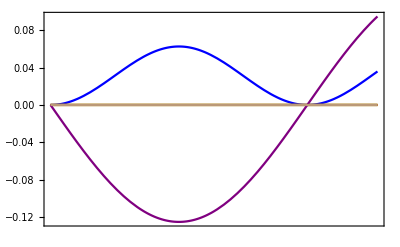

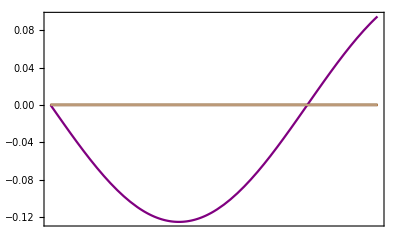

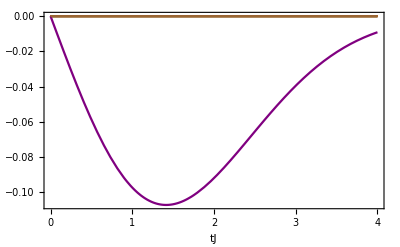

```mathematica
c[t_]:=1/4 corrsExact[π/2,t/2];
Plot[{c[t][[1,1]],c[t][[1,2]],c[t][[1,3]],c[t][[2,2]],c[t][[2,3]],c[t][[3,3]]},{t,0,4},PlotStyle->{Blue,Orange,Green,Red,Purple,Lighter@Brown},PlotRange->{{0,4},All},LabelStyle->Directive[FontSize->20],FrameTicks->{{Automatic,None},{{{1,""},{2,""},{3,""}},None}},FrameTicksStyle->Automatic,Frame->True]

c[t_]:=1/4 corrsSAll[π/2,t/2];
Plot[{c[t][[1,1]],c[t][[1,2]],c[t][[1,3]],c[t][[2,2]],c[t][[2,3]],c[t][[3,3]]},{t,0,4},PlotStyle->{Blue,Orange,Green,Red,Purple,Lighter@Brown},PlotRange->{{0,4},All},LabelStyle->Directive[FontSize->20],FrameTicks->{{Automatic,None},{{{1,""},{2,""},{3,""}},None}},Frame->True]

c[t_]:=1/4 corrsTWA[π/2,t/2];
Plot[{c[t][[1,1]],c[t][[1,2]],c[t][[1,3]],c[t][[2,2]],c[t][[2,3]],c[t][[3,3]]},{t,0,4},PlotStyle->{Blue,Orange,Green,Red,Purple,Brown},PlotRange->{{0,4},All},LabelStyle->Directive[FontSize->20],FrameTicks->{{Automatic,None},{Automatic,None}},Frame->True,FrameLabel->{{None,None},{Style["tJ",FontSize->20],None}}]
```

### Figure 9

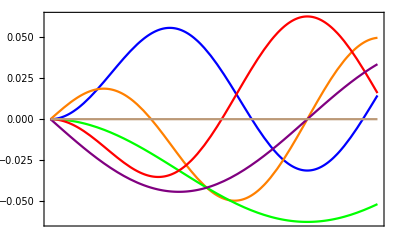

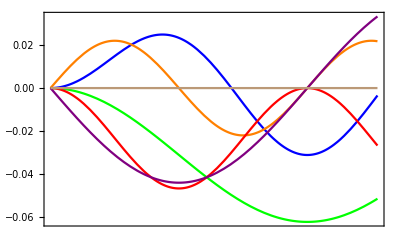

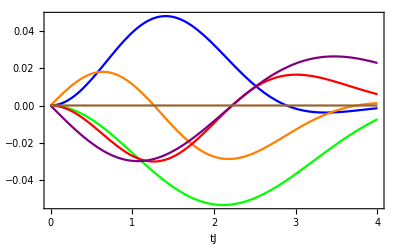

```mathematica
c[t_]:=1/4 corrsExact[π/4,t/2];
Plot[{c[t][[1,1]],c[t][[1,2]],c[t][[1,3]],c[t][[2,2]],c[t][[2,3]],c[t][[3,3]]},{t,0,4},PlotStyle->{Blue,Orange,Green,Red,Purple,Lighter@Brown},PlotRange->{{0,4},All},LabelStyle->Directive[FontSize->20],FrameTicks->{{Automatic,None},{{{1,""},{2,""},{3,""}},None}},FrameTicksStyle->Automatic,Frame->True]

c[t_]:=1/4 corrsSAll[π/4,t/2];
Plot[{c[t][[1,1]],c[t][[1,2]],c[t][[1,3]],c[t][[2,2]],c[t][[2,3]],c[t][[3,3]]},{t,0,4},PlotStyle->{Blue,Orange,Green,Red,Purple,Lighter@Brown},PlotRange->{{0,4},All},LabelStyle->Directive[FontSize->20],FrameTicks->{{Automatic,None},{{{1,""},{2,""},{3,""}},None}},Frame->True]

c[t_]:=1/4 corrsTWA[π/4,t/2];
Plot[{c[t][[1,1]],c[t][[1,2]],c[t][[1,3]],c[t][[2,2]],c[t][[2,3]],c[t][[3,3]]},{t,0,4},PlotStyle->{Blue,Orange,Green,Red,Purple,Brown},PlotRange->{{0,4},All},LabelStyle->Directive[FontSize->20],FrameTicks->{{Automatic,None},{Automatic,None}},Frame->True,FrameLabel->{{None,None},{Style["tJ",FontSize->20],None}}]
```

### Figure 10

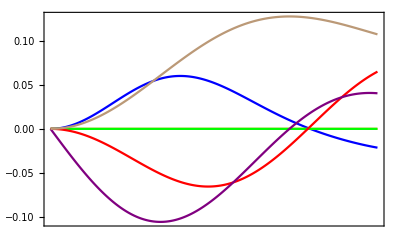

```mathematica
s=(KroneckerProduct@@Table[{{Cos[π/4.],Sin[π/4.]}},{i,10}])[[1]];
ts=Range[0.,4.,0.02];
f=onsiteOpsIsingED[s,10,-1./3,ts];
g=corrsIsingED[s,10,-1./3,ts];
cExact=Table[(g[[#,i,j]]+g[[#,j,i]])/2-f[[#,i]]f[[#,j]],{i,3},{j,3}]&/@Range[201];

ListPlot[{Transpose[{ts,cExact[[All,1,1]]}],Transpose[{ts,cExact[[All,1,2]]}],Transpose[{ts,cExact[[All,1,3]]}],Transpose[{ts,cExact[[All,2,2]]}],Transpose[{ts,cExact[[All,2,3]]}],Transpose[{ts,cExact[[All,3,3]]}]},Joined->True,PlotStyle->{Blue,Orange,Green,Red,Purple,Lighter@Brown},PlotRange->{{0,4},All},LabelStyle->Directive[FontSize->20],FrameTicks->{{Automatic,None},{{{1,""},{2,""},{3,""}},None}},FrameTicksStyle->Automatic,Frame->True]
```

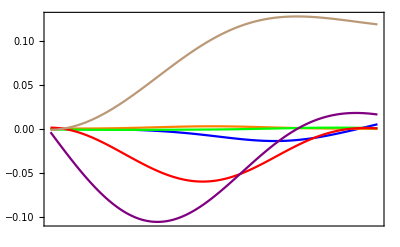

```mathematica
dtwa=dtwaEnsemble[π/2,10,SAll];
factors=scaleFactor[π/2,SAll];

ts=Range[0.,4.,0.02];
f=onSiteOpsIsing[dtwa,{SAll,factors},10,1./3,ts];
g=corrsIsing[dtwa,{SAll,factors},10,1./3,ts];
cAll=Table[(g[[#,i,j]]+g[[#,j,i]])/2-f[[#,i]]f[[#,j]],{i,3},{j,3}]&/@Range[201];

ListPlot[{Transpose[{ts,cAll[[All,1,1]]}],Transpose[{ts,cAll[[All,1,2]]}],Transpose[{ts,cAll[[All,1,3]]}],Transpose[{ts,cAll[[All,2,2]]}],Transpose[{ts,cAll[[All,2,3]]}],Transpose[{ts,cAll[[All,3,3]]}]},Joined->True,PlotStyle->{Blue,Orange,Green,Red,Purple,Lighter@Brown},PlotRange->{{0,4},All},LabelStyle->Directive[FontSize->20],FrameTicks->{{Automatic,None},{{{1,""},{2,""},{3,""}},None}},FrameTicksStyle->Automatic,Frame->True]
```

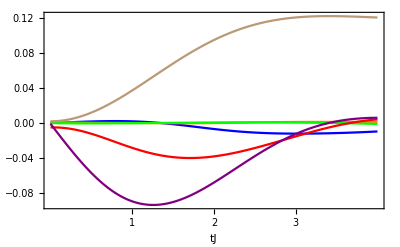

```mathematica
twa=twaEnsemble[π/2,10];
ts=Range[0.,4.,0.02];
f=onSiteOpsIsing[twa,10,1./3,ts];
g=corrsIsing[twa,10,1./3,ts];
ctwa=Table[(g[[#,i,j]]+g[[#,j,i]])/2-f[[#,i]]f[[#,j]],{i,3},{j,3}]&/@Range[201];

ListPlot[{Transpose[{ts,ctwa[[All,1,1]]}],Transpose[{ts,ctwa[[All,1,2]]}],Transpose[{ts,ctwa[[All,1,3]]}],Transpose[{ts,ctwa[[All,2,2]]}],Transpose[{ts,ctwa[[All,2,3]]}],Transpose[{ts,ctwa[[All,3,3]]}]},Joined->True,PlotStyle->{Blue,Orange,Green,Red,Purple,Lighter@Brown},PlotRange->{{0,4},All},LabelStyle->Directive[FontSize->20],FrameTicks->{{Automatic,None},{Range[3],None}},FrameLabel->{{None,None},{Style["tJ",FontSize->20],None}},FrameTicksStyle->Automatic,Frame->True]
```

### Figure 11

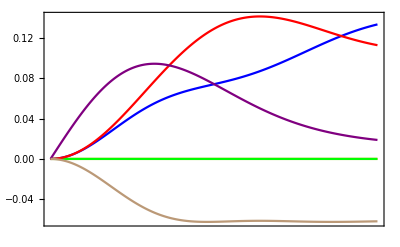

```mathematica
s=(KroneckerProduct@@Table[{{Cos[π/4.],Sin[π/4.]}},{i,10}])[[1]];
ts=Range[0.,4.,0.02];
Date[]
f=onsiteOpsXYED[s,10,ts];
Date[]
g=corrsXYED[s,10,ts];
Date[]
cExact=1/4 Table[(g[[#,i,j]]+g[[#,j,i]])/2-0f[[#,i]]f[[#,j]],{i,3},{j,3}]&/@Range[201]; (* g is already "connected". *)

ListPlot[{Transpose[{ts,cExact[[All,1,1]]}],Transpose[{ts,cExact[[All,1,2]]}],Transpose[{ts,cExact[[All,1,3]]}],Transpose[{ts,cExact[[All,2,2]]}],Transpose[{ts,cExact[[All,2,3]]}],Transpose[{ts,cExact[[All,3,3]]}]},Joined->True,PlotStyle->{Blue,Orange,Green,Red,Purple,Lighter@Brown},PlotRange->{{0,4},All},LabelStyle->Directive[FontSize->20],FrameTicks->{{Automatic,None},{{{1,""},{2,""},{3,""}},None}},FrameTicksStyle->Automatic,Frame->True]
```

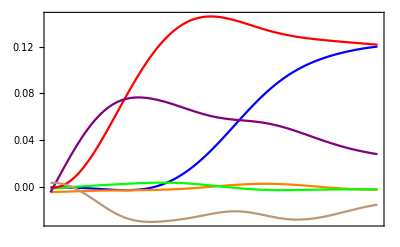

```mathematica
dtwa=dtwaEnsemble[π/2,10,SAll];
factors=scaleFactor[π/2,SAll];

ts=Range[0.,4.,0.02];
fdtwa=onSiteOpsXY[dtwa,{SAll,factors},10,ts];
gdtwa=corrsXY[dtwa,{SAll,factors},10,ts];
cAll=Table[(gdtwa[[#,i,j]]+gdtwa[[#,j,i]])/2-fdtwa[[#,i]]fdtwa[[#,j]],{i,3},{j,3}]&/@Range[201];

ListPlot[{Transpose[{ts,cAll[[All,1,1]]}],Transpose[{ts,cAll[[All,1,2]]}],Transpose[{ts,cAll[[All,1,3]]}],Transpose[{ts,cAll[[All,2,2]]}],Transpose[{ts,cAll[[All,2,3]]}],Transpose[{ts,cAll[[All,3,3]]}]},Joined->True,PlotStyle->{Blue,Orange,Green,Red,Purple,Lighter@Brown},PlotRange->{{0,4},All},LabelStyle->Directive[FontSize->20],FrameTicks->{{Automatic,None},{{{1,""},{2,""},{3,""}},None}},FrameTicksStyle->Automatic,Frame->True]
```

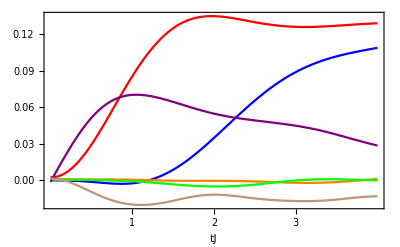

```mathematica
twa=twaEnsemble[π/2,10];
ts=Range[0.,4.,0.02];
ftwa=onSiteOpsXY[twa,10,ts];
gtwa=corrsXY[twa,10,ts];
ctwa=Table[(gtwa[[#,i,j]]+gtwa[[#,j,i]])/2-ftwa[[#,i]]ftwa[[#,j]],{i,3},{j,3}]&/@Range[201];

ListPlot[{Transpose[{ts,ctwa[[All,1,1]]}],Transpose[{ts,ctwa[[All,1,2]]}],Transpose[{ts,ctwa[[All,1,3]]}],Transpose[{ts,ctwa[[All,2,2]]}],Transpose[{ts,ctwa[[All,2,3]]}],Transpose[{ts,ctwa[[All,3,3]]}]},Joined->True,PlotStyle->{Blue,Orange,Green,Red,Purple,Lighter@Brown},PlotRange->{{0,4},All},LabelStyle->Directive[FontSize->20],FrameTicks->{{Automatic,None},{Range[3],None}},FrameLabel->{{None,None},{Style["tJ",FontSize->20],None}},FrameTicksStyle->Automatic,Frame->True]
```

### Movie for transverse Ising (the 2 movies made by Kenneth for pure Ising are correct)

```mathematica
plot[corrs_,p_?NumericQ,t_,approxNames_]:=Module[{r,polynomial,p1,p5},
r={x,y,z}-bv;
(polynomial=(r.(corrs[[#]]).r)/(1+(r.r)^(3/2)/czoom^3);
Clear[x,y,z];
(*Generating the CMV*)
p1=plot[polynomial,p, Red]; (*graphs the figure*)
Clear[x,y,z];
p5=plot[polynomial,-p, Blue]; (*graphs the figure*)
Clear[x,y,z];
 Show[p0,p1,p5,Graphics3D[{Text[Style["x",Bold,30],{20,0,1}],Text[Style["y",Bold,30],{0,20,1}],Text[Style["z",Bold,30],{1,0,20}],Text[Style[approxNames[[#]],Bold,30],{10,-5,20}],Text[Style["t: "<>t,Bold,30],{-15,0,15}]}],ImageSize->Medium,Spacings->{0,0}])&/@Range[3]];
```

```mathematica
s=(KroneckerProduct@@Table[{{Cos[π/4.],Sin[π/4.]}},{i,10}])[[1]];
ts=Range[0.,3.9,0.1];
f=onsiteOpsIsingED[s,10,-1./3,ts];
g=corrsIsingED[s,10,-1./3,ts];
cExact=Re[Table[(g[[#,i,j]]+g[[#,j,i]])/2-f[[#,i]]f[[#,j]],{i,3},{j,3}]&/@Range[40]];

dtwa=dtwaEnsemble[π/2,10,SAll];
factors=scaleFactor[π/2,SAll];

ts=Range[0.,4.,0.1];
f=onSiteOpsIsing[dtwa,{SAll,factors},10,1./3,ts];
g=corrsIsing[dtwa,{SAll,factors},10,1./3,ts];
cAll=Re[Table[(g[[#,i,j]]+g[[#,j,i]])/2-f[[#,i]]f[[#,j]],{i,3},{j,3}]&/@Range[40]];

twa=twaEnsemble[π/2,10];
ts=Range[0.,4.,0.1];
f=onSiteOpsIsing[twa,10,1./3,ts];
g=corrsIsing[twa,10,1./3,ts];
ctwa=Re[Table[(g[[#,i,j]]+g[[#,j,i]])/2-f[[#,i]]f[[#,j]],{i,3},{j,3}]&/@Range[40]];
```

```mathematica
Export["/Users/bhuvaneshsundar/Desktop/research/TWA/paper/BhuvaneshFigures/transIsingMovie.mov",plot[{cExact[[#]],cAll[[#]],ctwa[[#]]},0.002,ToString[ts[[#]]],{"Exact","dTWA","TWA"}]&/@Range[40]];
```

### Movie for XX model

```mathematica
s=(KroneckerProduct@@Table[{{Cos[π/4.],Sin[π/4.]}},{i,10}])[[1]];
ts=Range[0.,3.9,0.1];
g=corrsXYED[s,10,ts];
cExact2=1/4 Re[Table[(g[[#,i,j]]+g[[#,j,i]])/2,{i,3},{j,3}]&/@Range[40]]; (* g is already the "connected correlation". *)

dtwa=dtwaEnsemble[π/2,10,SAll];
factors=scaleFactor[π/2,SAll];

ts=Range[0.,3.9,0.1];
f=onSiteOpsXY[dtwa,{SAll,factors},10,ts];
g=corrsXY[dtwa,{SAll,factors},10,ts];
cAll2=Re[Table[(g[[#,i,j]]+g[[#,j,i]])/2-f[[#,i]]f[[#,j]],{i,3},{j,3}]&/@Range[40]];

twa=twaEnsemble[π/2,10];
ts=Range[0.,3.9,0.1];
f=onSiteOpsXY[twa,10,ts];
g=corrsXY[twa,10,ts];
ctwa2=Re[Table[(g[[#,i,j]]+g[[#,j,i]])/2-f[[#,i]]f[[#,j]],{i,3},{j,3}]&/@Range[40]];
```

```mathematica
Export["/Users/bhuvaneshsundar/Desktop/research/TWA/paper/BhuvaneshFigures/XYMovie.mov",plot[{cExact2[[#]],cAll2[[#]],ctwa2[[#]]},0.002,ToString[ts[[#]]],{"Exact","dTWA","TWA"}]&/@Range[40]];
```